# Project Coding Template APPM 2350 : Spring 2018 Authors: Mattias Leino Derek Thomas

Hi everyone!
The purpose of this document is to show you how a Mathematica notebook can be organized for easier legibility. It might make it is easier to understand the flow of your work this way.

For the 1st project I recommend copying the coaster template code into the first section below and starting by reviewing the Crash Course file!

```mathematica
Clear["Global`*"]
```

## Section 3: Observers at three different latitudes

```mathematica
(* Functions *)
Θ[t_] := -0.41 * Cos[(2π*t)/ 365.25]
x[t_,ϕ_] := Cos[ϕ] * Sin[2π*t]
y[t_,ϕ_] := -Cos[ϕ] * Cos[2π*t] * Cos[Θ[t]] + Sin[ϕ] * Sin[Θ[t]]
z[t_, ϕ_] := Cos[ϕ] * Cos[2π * t] * Sin[Θ[t]] + Sin[ϕ] * Cos[Θ[t]]
n[t_,ϕ_] := Cos[ϕ] * Sin[Θ[t]] + Sin[ϕ] * Cos[Θ[t]] * Cos[2 * π * t]
e[t_, ϕ_] := Cos[Θ[t]] * Sin[2 * π * t]
u[t_, ϕ_] := (1 - n[t,ϕ]^2 - e[t,ϕ]^2)^(1/2)
η[t_, ϕ_] := ArcSin[u[t,ϕ]]
```

```mathematica
(* Latitudes of the locations we are looking at *)
boulderLat = 0.6981;
chichenitzaLat = 0.3613;
southpoleLat = 1.5708;
```

This is a plot of the position of the sun above and below the horizon (y=0) over the course of 5 days.

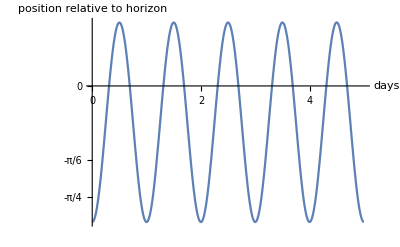

```mathematica
Plot[{y[t,0.698132]},{t,0,5}, AxesLabel->{"days","position relative to horizon"}, Ticks->{{0,1,2,3,4,5},{-π/4, -π/6,0,π/6,π/4}}]
```

```mathematica
(* Using the FindRoot fucntion to build a table of all the times the y(t,ϕ) function finds zero. i.e. When the sun crosses the horizon, either sunrise or sunset *)
days ={t} /. Table[FindRoot[y[t,boulderLat]==0, {t, day -0.25}], {day, 0.5, 365,0.5}] ;


(*creates a list of day lengths *)
riseIndex = 1;
setIndex = 2;
rise = 0;
set = 0;
dayLengths = {};
While[riseIndex < 730, 
rise = Part[days,riseIndex]; 
set = Part[days, setIndex]; 
AppendTo[dayLengths,(set-rise)];
 riseIndex = riseIndex+2; setIndex = setIndex+2];

(*some tests + printing min and max*)
dayLengths;
Length[dayLengths];
Max[dayLengths]
Position[dayLengths,Max[dayLengths]]
Min[dayLengths]
Position[dayLengths,Min[dayLengths]]

(* find the closest absolute distance to .5 *)
findEquinox[loopStart_,loopEnd_] :=(
candidate = 0;
currentMin =1;
For[i=loopStart, i < loopEnd, i++,
candidate = Part[dayLengths,i];
currentMin = If[(Abs[.5 - candidate]) < (Abs[.5-currentMin]), candidate, currentMin]
]
Return[currentMin];
)
equinox = findEquinox[1,180];
```

0.618818

{{183,1}}

0.381186

{{1,1}}

0.618826

{{183,1}}

0.381178

{{1,1}}

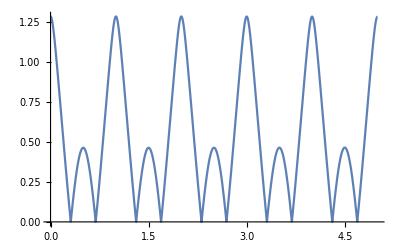

```mathematica
Plot[{η[t,0.698132]},{t,0,5}]
```

```mathematica
RiseAngle[dayRA_,phiRA_] := 
(srtRA = FindRoot[y[tRA, phiRA] == 0, {tRA, Round[dayRA] -0.75}];
180*ArcCos[n[tRA/.srtRA,phiRA]]/Pi);
```

```mathematica
boulderRA = Table[RiseAngle[dayRA,40*Pi/180],{dayRA,0,365,1}];
```

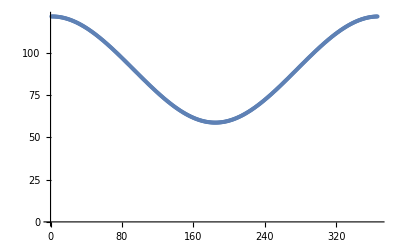

```mathematica
ListPlot[boulderRA]
```

```mathematica
mexicoDays ={t} /. Table[FindRoot[y[t,chichenitzaLat]==0, {t, day -0.25}], {day, 0.5, 365,0.5}] ;


(*creates a list of day lengths *)
riseIndex = 1;
setIndex = 2;
rise = 0;
set = 0;
dayLengths = {};
While[riseIndex < 730, 
rise = Part[mexicoDays,riseIndex]; 
set = Part[mexicoDays, setIndex]; 
AppendTo[dayLengths,(set-rise)];
 riseIndex = riseIndex+2; setIndex = setIndex+2];

(*some tests + printing min and max*)
dayLengths;
Length[dayLengths];
Max[dayLengths]
Position[dayLengths,Max[dayLengths]]
Min[dayLengths]
Position[dayLengths,Min[dayLengths]]

(* find the closest absolute distance to .5 *)
findEquinox[loopStart_,loopEnd_] :=(
candidate = 0;
currentMin =1;
For[i=loopStart, i < loopEnd, i++,
candidate = Part[dayLengths,i];
currentMin = If[(Abs[.5 - candidate]) < (Abs[.5-currentMin]), candidate, currentMin]
]
Return[currentMin];
)
equinox = findEquinox[1,180];
```

0.552517

{{183,1}}

0.447485

{{1,1}}

```mathematica
southPoleDays ={t} /. Table[FindRoot[y[t,southpoleLat]==0, {t, day -0.25}], {day, 0.5, 365,0.5}] ;

(*creates a list of day lengths *)
riseIndex = 1;
setIndex = 2;
rise = 0;
set = 0;
dayLengths = {};
While[riseIndex < 730, 
rise = Part[southPoleDays,riseIndex]; 
set = Part[southPoleDays, setIndex]; 
AppendTo[dayLengths,(set-rise)];
 riseIndex = riseIndex+2; setIndex = setIndex+2];

(*some tests + printing min and max*)
dayLengths;
Length[dayLengths];
Max[dayLengths]
Position[dayLengths,Max[dayLengths]]
Min[dayLengths]
Position[dayLengths,Min[dayLengths]]

(* find the closest absolute distance to .5 *)
findEquinox[loopStart_,loopEnd_] :=(
candidate = 0;
currentMin =1;
For[i=loopStart, i < loopEnd, i++,
candidate = Part[dayLengths,i];
currentMin = If[(Abs[.5 - candidate]) < (Abs[.5-currentMin]), candidate, currentMin]
]
Return[currentMin];
)
equinox = findEquinox[1,180];
```

730.5

{{186,1}}

-3469.87

{{182,1}}

# Appendix

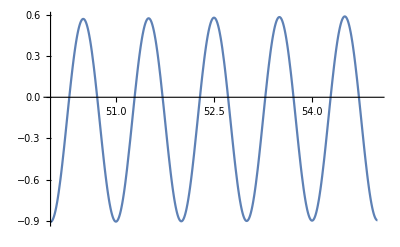

```mathematica
Plot[{y[t,0.698132]},{t,50,55}]
```

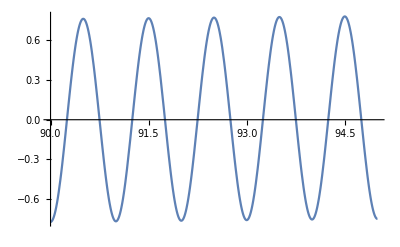

```mathematica
Plot[{y[t,0.698132]},{t,90,95}]
```

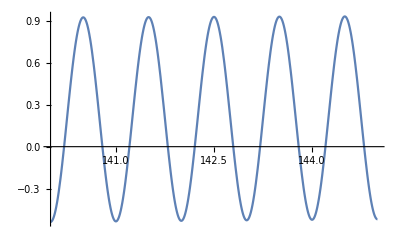

```mathematica
Plot[{y[t,0.698132]},{t,140,145}]
```

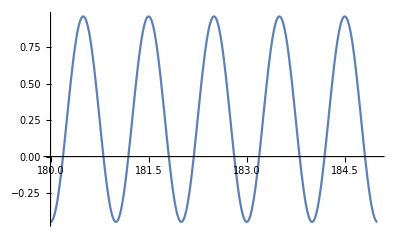

```mathematica
Plot[{y[t,0.698132]},{t,180,185}]
```

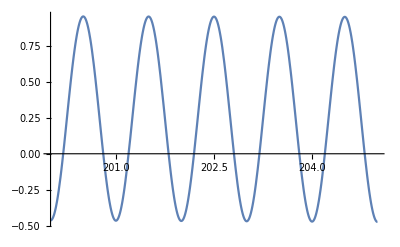

```mathematica
Plot[{y[t,0.698132]},{t,200,205}]
```

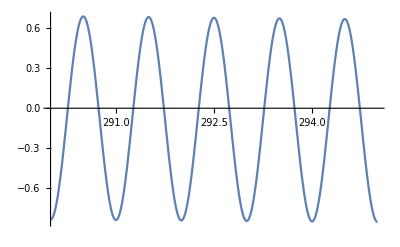

```mathematica
Plot[{y[t,0.698132]},{t,290,295}]
```

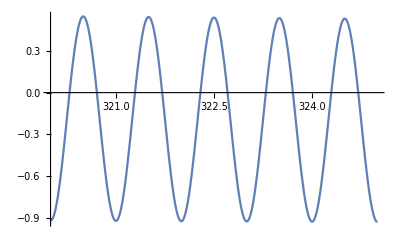

```mathematica
Plot[{y[t,0.698132]},{t,320,325}]
```